```mathematica
c= 0.25;
b=4;
size=0.8;
ψ[z_] = -c Exp[ -c-I  z];
W[z_?NumericQ] := ProductLog[0,ψ[z]];
F1[z_] = -c-W[b z];
F2[z_] = -c-ψ[b z]Exp[-W[b^2 z]];
F3[z_?NumericQ] = -c-ψ[b z]Exp[-ψ[b^2 z]Exp[-W[b^3 z]]];
F3b[z_?NumericQ] = -c-ψ[b z]Exp[-ψ[b^2 z]];
F4[z_?NumericQ] = -c-ψ[b z]Exp[-ψ[b^2 z]Exp[-ψ[b^3 z]Exp[-W[b^4 z]]]];
F5[z_?NumericQ] := -c-ψ[b z]Exp[-ψ[b^2 z]Exp[-ψ[b^3 z]Exp[-ψ[b^4 z]Exp[-W[b^5 z]]]]];
F6[z_?NumericQ] := -c-ψ[b z]Exp[-ψ[b^2 z]Exp[-ψ[b^3 z]Exp[-ψ[b^4 z]Exp[-ψ[b^5 z]Exp[-W[b^6 z]]]]]];
cplot =ComplexPlot[F4[z],{z,-size/2-size I/4,size/2+size/1.3333 I},ColorFunction->{"CyclicArg","CyclicLogAbs"},PlotPoints->150,MaxRecursion->6,PerformanceGoal->"Quality",AxesLabel->{"Re z","Im z"},Axes->True, PlotLabel->"vi) c=" <> ToString[c]<>", β="<>ToString[b](*,PlotLegends->BarLegend[Automatic,LegendLabel->Placed[Subscript[F,η][z],Above]]*)]
```

-Graphics-

```mathematica
Export["vi nobar.png",cplot,ImageResolution->600]
```

vi nobar.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["iv.png"]]]
```

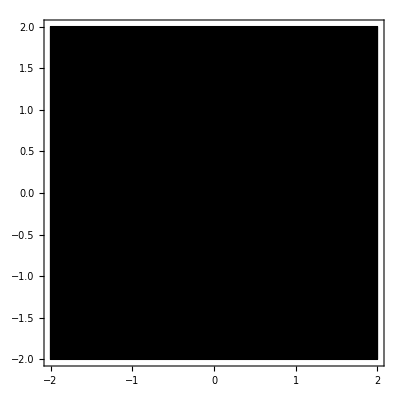

```mathematica
ComplexPlot[Exp[-I 2π z]-1,{z,-2-2 I,2+2 I},ColorFunction->{"CyclicArg","CyclicLogAbs"},PlotPoints->150,MaxRecursion->6,PerformanceGoal->"Quality",PlotLegends->BarLegend[Automatic,LegendLabel->Placed["F(z): Abs and Arg",Right,Rotate[#,90 Degree]&],LegendLabel->Placed["legend",Left]]]
```

```mathematica
d=0.3
beta=1.7
ComplexPlot[-d+(1-d)Sum[d^n Exp[-I z Sum[beta^j,{j,1,n}]],{n,1,10}],{z,-1-I,1+I}]
```

0.3

1.7

-Graphics-

```mathematica
Sum[bt^j,{j,1,N}]
```

(bt (-1+bt^N))/(-1+bt)

```mathematica
Clear[SafF];
c=0.3;
b=1.7;
size=1;

ψ[z_]:=-c Exp[-c-I z];
W[z_]:=ProductLog[0,ψ[z]];

F6[z_?NumericQ]:=-c-ψ[b z] Exp[-ψ[b^2 z] Exp[-ψ[b^3 z] Exp[-ψ[b^4 z] Exp[-ψ[b^5 z] Exp[-W[b^6 z]]]]]];

SafF[z_?NumericQ]:=Quiet@Check[Module[{val=F6[z]},If[NumberQ[val]&& Abs[val]<10^(1000000),val,Indeterminate]],Indeterminate];


ComplexPlot[SafF[z],{z,-size-0.5 I,size+size I},ColorFunction->"CyclicLogAbs",PlotPoints->200,MaxRecursion->6,PerformanceGoal->"Quality"]
```

-Graphics-